# Kelvin Problem in 2-d plane strain

```mathematica
x = xo - xs
y = yo - ys
C0 = 1/ (4 * Pi *(1-nu))
r = Sqrt[x^2 + y^2]
g = -C0 * Log[r]
gx = -C0*x/r^2
gy = -C0*y/r^2
ux = fx/(2*mu)*((3-4*nu)*g - x*gx) + fy/(2*mu)*(-y*gx)
uy = fx/(2*mu)*(-x*gy) + fy/(2*mu)*((3-4*nu)*g -y*gy)
```

xo-xs

yo-ys

1/(4 (1-nu) π)

√((xo-xs)^2+(yo-ys)^2)

-Log[√((xo-xs)^2+(yo-ys)^2)]/(4 (1-nu) π)

-(xo-xs)/(4 (1-nu) π ((xo-xs)^2+(yo-ys)^2))

-(yo-ys)/(4 (1-nu) π ((xo-xs)^2+(yo-ys)^2))

-(fy (xo-xs) (-yo+ys))/(8 mu (1-nu) π ((xo-xs)^2+(yo-ys)^2))+(fx ((xo-xs)^2/(4 (1-nu) π ((xo-xs)^2+(yo-ys)^2))-((3-4 nu) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 (1-nu) π)))/(2 mu)

-(fx (-xo+xs) (yo-ys))/(8 mu (1-nu) π ((xo-xs)^2+(yo-ys)^2))+(fy ((yo-ys)^2/(4 (1-nu) π ((xo-xs)^2+(yo-ys)^2))-((3-4 nu) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 (1-nu) π)))/(2 mu)

```mathematica
uxmod = ReplaceAll[ux,{ys->0,yo->0}]
uxint = Integrate[uxmod,{xs,-1,1},GenerateConditions->False]
```

(fx (1/(4 (1-nu) π)-((3-4 nu) Log[√((xo-xs)^2)])/(4 (1-nu) π)))/(2 mu)

-(fx (4+(-3+4 nu) (-4-(-1+xo) Log[(-1+xo)^2]+(1+xo) Log[(1+xo)^2])))/(16 mu (-1+nu) π)

0.0265258 (4-2. (-4-(-1+xo) Log[(-1+xo)^2]+(1+xo) Log[(1+xo)^2]))

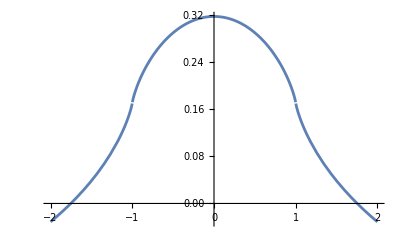

```mathematica
uplot = ReplaceAll[uxint,{fx -> 1, mu->1,nu->0.25}]
Plot[uplot,{xo,-2,2}]
```

```mathematica
uxmod2 = ReplaceAll[ux, { mu->1,nu->0.25}]
uxint2 = Integrate[uxmod2,{xs,-1,1},{ys,-1,1}]
```

-(0.0530516 fy (xo-xs) (-yo+ys))/((xo-xs)^2+(yo-ys)^2)+1/2 fx ((0.106103 (xo-xs)^2)/((xo-xs)^2+(yo-ys)^2)-0.212207 Log[√((xo-xs)^2+(yo-ys)^2)])

0.0265258 (4-2 (1+2 (-1+xo) xo) ArcTan[1-xo]-2 (1+2 xo (1+xo)) ArcTan[1+xo]+ⅈ Log[(-1+ⅈ)-xo]-(2+ⅈ xo) xo Log[(-1+ⅈ)-xo]-ⅈ Log[(1+ⅈ)-xo]+(2+ⅈ xo) xo Log[(1+ⅈ)-xo]-ⅈ (ⅈ+xo)^2 Log[(-1+ⅈ)+xo]+ⅈ (ⅈ+xo)^2 Log[(1+ⅈ)+xo]-2 xo Log[2+(-2+xo) xo]-4. (-6+ArcCot[1-xo]+ArcCot[1+xo]+2 ArcTan[1-xo]+2 ArcTan[1+xo]+2 xo Log[-1+xo]-(-1+xo) Log[(-1+xo)^2]+1/2 ⅈ ((-ⅈ+xo)^2 Log[(1+ⅈ)-xo]-(ⅈ+xo)^2 Log[(-1+ⅈ)+xo])-2 xo Log[1+xo]+(1+xo) Log[(1+xo)^2]+1/2 ⅈ (-(-ⅈ+xo)^2 Log[(-1+ⅈ)-xo]+(ⅈ+xo)^2 Log[(1+ⅈ)+xo])-xo Log[2-2 xo+xo^2]+Log[(2-2 xo+xo^2)/(-1+xo)^2]+xo Log[2+2 xo+xo^2]+Log[(2+2 xo+xo^2)/(1+xo)^2]-xo (2 ArcCot[1-xo]-2 ArcCot[1+xo]+2 xo (ArcTan[1-xo]+ArcTan[1+xo])+Log[2+(-2+xo) xo]-Log[2+xo (2+xo)]))+2 xo Log[2+xo (2+xo)])

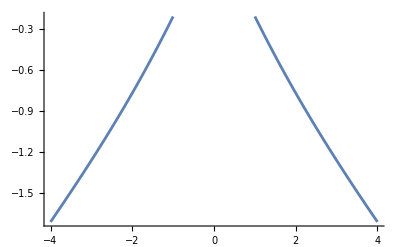

```mathematica
uplot2 = ReplaceAll[uxint2,{fx -> 1, fy -> 0}]
Plot[uplot2,{xo,-4,4}]
(*ContourPlot[uxint2,{xo,-2,2},{yo,-2,2}]*)
```